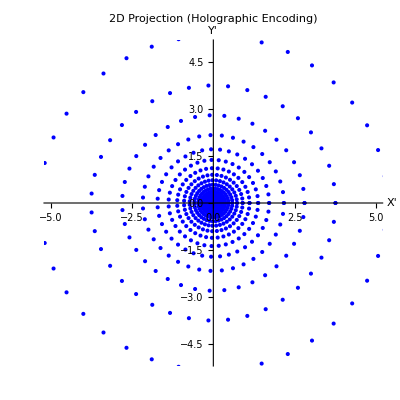

```mathematica
(*Define the parametric surface function*)ParametricSurface[u_,v_,shape_]:=Switch[shape,"sphere",{Sin[u] Cos[v],Sin[u] Sin[v],Cos[u]},"cone",Module[{k=1,r=u},{r Cos[v],r Sin[v],k r}],"paraboloid",Module[{r=u},{r Cos[v],r Sin[v],r^2}],_,Throw["Unknown shape: Choose 'sphere', 'cone', or 'paraboloid'"]];

(*Define the stereographic projection function*)
StereographicProjection[x_,y_,z_]:=If[1-z==0,Nothing,{x/(1-z),y/(1-z)}];

(*Define the inverse projection function*)
InverseProjection[xProj_,yProj_,shape_]:=Module[{rProj=Sqrt[xProj^2+yProj^2]},Switch[shape,"sphere",Module[{denom=1+rProj^2},{(2 xProj)/denom,(2 yProj)/denom,(1-rProj^2)/denom}],"cone",{xProj,yProj,rProj},"paraboloid",{xProj,yProj,rProj^2},_,Throw["Unknown shape: Choose 'sphere', 'cone', or 'paraboloid'"]]];

(*Select shape*)
shapeType="cone"; (*Change this to test different shapes*)

(*Generate a parametric surface*)
uRes=20;vRes=40; (*Reduced resolution for better grid visibility*)
u=If[shapeType=="sphere",Subdivide[0.01,Pi,uRes-1],Subdivide[0,1,uRes-1]];
v=Subdivide[0,2 Pi,vRes-1];

(*Create meshgrid using Table*)
{uMesh,vMesh}=Transpose[Flatten[Table[{u[[i]],v[[j]]},{i,1,uRes},{j,1,vRes}],1]];

(*Compute parametric surface*)
{x,y,z}=Transpose[ParametricSurface@@@Transpose[{uMesh,vMesh,ConstantArray[shapeType,Length[uMesh]]}]];

(*Apply stereographic projection and filter invalid points*)
{xProjFiltered,yProjFiltered}=Transpose[DeleteCases[StereographicProjection@@@Transpose[{x,y,z}],Nothing]];

(*Reconstruct the surface using inverse projection*)
{xRecon,yRecon,zRecon}=Transpose[InverseProjection@@@Transpose[{xProjFiltered,yProjFiltered,ConstantArray[shapeType,Length[xProjFiltered]]}]];

(*Reshape reconstructed points into 2D arrays*)
{xRecon2D,yRecon2D,zRecon2D}=ArrayReshape[#,{uRes,vRes}]&/@{xRecon,yRecon,zRecon};

(*Create figure with 3 subplots*)
(*Final output*)GraphicsRow[{(*Original 3D Surface*)ParametricPlot3D[ParametricSurface[u,v,shapeType],{u,0.01,Pi},{v,0,2 Pi},PlotStyle->Cyan,BoxRatios->{1,1,1},AxesLabel->{"X","Y","Z"},Mesh->All,PlotLabel->"Original 3D "<>ToUpperCase[shapeType]],(*2D Projection*)ListPlot[Transpose[{xProjFiltered,yProjFiltered}],PlotStyle->Blue,PlotRange->{{-5,5},{-5,5}},AspectRatio->1,AxesLabel->{"X'","Y'"},PlotLabel->"2D Projection (Holographic Encoding)"],(*Reconstructed 3D Surface*)Graphics3D[{Red,Thick,Line[Table[Table[{xRecon2D[[i,j]],yRecon2D[[i,j]],zRecon2D[[i,j]]},{j,1,vRes}],{i,1,uRes}]],Line[Table[Table[{xRecon2D[[i,j]],yRecon2D[[i,j]],zRecon2D[[i,j]]},{i,1,uRes}],{j,1,vRes}]]},BoxRatios->{1,1,1},Axes->True,AxesLabel->{"X","Y","Z"},PlotLabel->"Reconstructed 3D "<>ToUpperCase[shapeType]]},ImageSize->Full]
```